LAKE POLLUTION MODEL

C'[t]==-(F C[t])/V+(F c_in)/V

{{C[t]→ⅇ^(-(F t)/V) (c0-c_in+ⅇ^((F t)/V) c_in)}}

{{C[t]→ⅇ^(-t/7) (-1000000+4000000 ⅇ^(t/7))}}

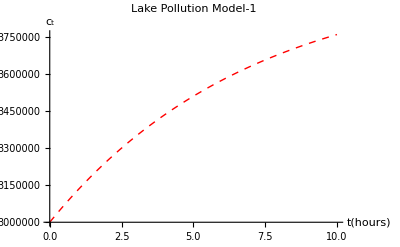

```mathematica
DE=C'[t]== F/V Subscript[c, in] - F/V C[t]
soln=DSolve[{DE,C[0]==c0},C[t],t]
soln/.{Subscript[c, in]->4*10^6,V->28*10^6,F->4*10^6,c0->3*10^6}
Plot[
Evaluate[C[t]/.soln/.{Subscript[c, in]->4*10^6,V->28*10^6,F->4*10^6,c0->3*10^6}],{t,0,10},AxesLabel->{t[hours],C[t]},AxesStyle->Arrowheads[{0,0.05}],PlotStyle->{Red,Thick,Dashed},PlotLabel->"Lake Pollution Model-1"]
```

C'[t]==-(F C[t])/V+(F c_in)/V

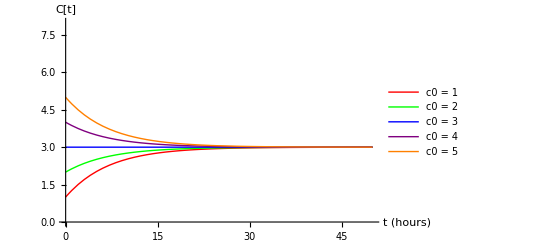

```mathematica
DE=C'[t]==F/V Subscript[c, in] - F/V C[t]
soln=DSolve[{DE,C[0]==c0},C[t],t];

plots=Table[
Evaluate[
C[t]/. First[soln]/.{Subscript[c, in]-> 3,V->28,F->4,c0->c0val}],{c0val,1,5}];
Plot[plots,{t,0,50},AxesLabel->{"t (hours)","C[t]"},PlotRange->{0,8},AxesStyle->Arrowheads[{0,0.04}],PlotLegends->Placed[LineLegend[Automatic,Table["c0 = "<>ToString[i],{i,1,5}]],Below],PlotStyle->{Red,Green,Blue,Purple,Orange}]
```

Interpretation of Graph :- As the time increase the concentration of pollutants in the lake will 
approach the concentration of the polluted water entering the lake [ C[t] = cin] Here c0 = cin then 
the level of pollution in the lake decreases monotonically to cin . If c0<cin then the level of pollution 
in the lake increase monotonically to cin.